ex 7.1

```mathematica
f[n_]:=((4+n)*.997^n+(4+6n)(1-.997^n))/n
```

```mathematica
Solve[f'[n]==0,n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→-15.9318},{n→16.7331}}

```mathematica
Plot[f[n],{n,0,30}]
```

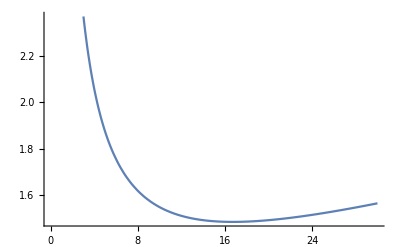

```mathematica
n=16.7331
```

```mathematica
16.7331
```

```mathematica
f[r_]:=((4+n)*r^n+(4+6n)(1-r^n))/n
```

```mathematica
Function[r,((4+n) r^n+(4+6 n) (1-r^n))/n]
```

Function[r,((4+n) r^n+(4+6 n) (1-r^n))/n]

Sensitivity

```mathematica
f[r]
```

0.0597618 (20.7331 r^16.7331+104.399 (1-r^16.7331))

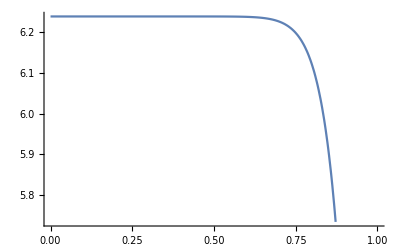

```mathematica
Plot[f[r],{r,0,1}]
```

#### 7.5.1

A

```mathematica
A[x_]:=(4/x+6-5(.997)^x)
```

```mathematica
A[x]
```

6-5 0.997^x+4/x

```mathematica
Together[6-5 0.997^x+4/x]
```

-(-4-6 x+5 0.997^x x)/x

```mathematica
Solve[A'[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

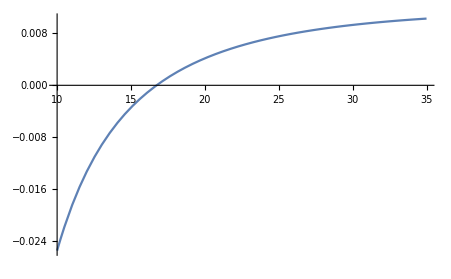

```mathematica
Plot[A'[x], {x,10,35}]
```

The derivative goes from negative to positive, therefore minimum

B

```mathematica
FindRoot[A'[x],{x,20}]
```

{x→16.7331}

C

```mathematica
A[16.73305471208393]
```

1.48421

D

```mathematica
A[10]
```

1.54799

```mathematica
A[35]
```

1.61337

The max will be x=35 or 1.61337